```mathematica
Manipulate[
Module[{t,w,L,u,ν,ρ,μ,ka,Cp,Pr,Rex,h,P,Ac,k,Tb,m,qf,T,xT,col},
t=0.0015;(*m thickness*)
w=0.02;(*width*)
L:=length/1000;(*length*)

(*air properties*)
u=2;(*m/s*)
ν=1.71*^-5;(*m2/s*)
ρ=1.164;(*kg/m3*)
μ:=ν*ρ;(*N s/m2*)
ka=0.0264;(*W/m/K*)
Cp=1005;(*J/kg/K*)

Pr:=(Cp*μ)/ka;
Rex:=(u*If[fin==1,w,t])/ν;
h:=ha/.First@If[fin==1,Solve[(ha*w)/ka==0.664*Rex^(1/2)*Pr^(1/3),ha],Solve[(ha*t)/ka==0.683*Rex^0.466*Pr^(1/3),ha]];

If[fin==1,{P:=2*w+2*t;Ac:=w*t},{P:=π*t;Ac:=π*t^2/4;}];

(*therm. data*)
k:=Which[
mat==1,14,(*s.steel*)
mat==2,60.5,(*carbon steel*)
mat==3,80.2,(*iron*)
mat==4,110,(*brass*)
mat==5,237,(*aluminum*)
mat==6,401(*copper*)
];(*W/m/K*)

Tb=500;
m:=√((h*P)/(k*Ac));
(*m:={√((h*P)/(k*Ac)),√((If[fin==1,2,4]*h)/(k*t)),√((If[fin==1,2,4]*h)/(k*Ac))};*)
qf:=(Tb-Ta)*√(h*P*k*Ac)*Tanh[m*L];
T[x_]:=(Tb-Ta)*Cosh[m*(L-x)]/Cosh[m*L]+Ta;

xT:=Evaluate@Interpolation[Transpose[{Range[500,273,-1],Evaluate@Table[x/.Quiet@FindRoot[250+23.72*Cosh[152.3*(1/50-x)]==t,{x,0}],{t,273,500,1}]}]];
col[x_]:=ColorData["TemperatureMap"][Rescale[xT[T[x]],{0,0.02}]];

(*DensityPlot[xT[y],{x,0,1},{y,273,500},ColorFunction->"TemperatureMap",PlotPoints->30,
Epilog->{Line[{{-0.5,T[L]},{1,T[L]}}],Text[Style[NumberForm[T[L],{3,0}],17],{-0.5,T[L]},{1,0}]},
PlotRange->{{-1,1},{273,500}},PlotRangePadding->{{0.1,None},5},Frame->{{None,True},{None,None}},FrameTicks->All,FrameStyle->Black,LabelStyle->17,AspectRatio->Full,ImageSize->{150,315}]*)

Grid[{
{Text@Style[Column[{
Row[{"fin heat transfer rate = ",NumberForm[qf,{3,2}]," W"}],
Row[{"temperature of fin tip = ",NumberForm[T[L],{3,0}]," K"}]
},Alignment->"="],17],SpanFromLeft},
{(*Graphics3D[{
{GrayLevel[0.4],Tube[{{0,0,0.25},{0,0,1}},0.05],Tube[{{0,0,0},{0,0,0.25}},{0.01,0.05}]},
{Blue,CapForm["Butt"],Tube[{{0,0,1},{0,0,1.2}},{0.5,0.2}],Tube[{{0,0,1.2},{0,0,1.8}},{0.2,0.125}],Tube[{{0,0,1.8},{0,0,2}},{0.125,0.3}]}
},Boxed->False,ViewPoint->Front,ImageSize->{100,315}(*,PlotRange->{{-0.5,0.5},{-0.5,0.5},{0,2}}*)],*)
Show[
Graphics3D[{{col[0],Cuboid[{-0.0025,-w/2,-w/2},{0,w/2,w/2}]},Text[Style["base = 500 K",18],{0,0,0.0075},{0,0},{2,0.35}]}],
Switch[fin,
1,RegionPlot3D[z<t,{x,0,L},{y,-w/2,w/2},{z,0,t},Mesh->None,ColorFunction->(col[#1]&),ColorFunctionScaling->False],
2,Show[Graphics3D[{col[L],Cylinder[{{0.999*L,0,0},{L,0,0}},t/2]}],ParametricPlot3D[{x,t/2*Sin[θ],t/2*Cos[θ]},{θ,0,2*π},{x,0,L},Mesh->None,ColorFunction->(col[#1]&),ColorFunctionScaling->False]]
],Boxed->False,ViewPoint->{2,-2,1},Lighting->"Neutral",ImageSize->{300,315}],
DensityPlot[xT[y],{x,0,1},{y,273,500},ColorFunction->"TemperatureMap",PlotPoints->30,
Epilog->{Line[{{-0.5,T[L]},{1,T[L]}}],Text[Style[NumberForm[T[L],{3,0}],17],{-0.5,T[L]},{1,0}]},
PlotRange->{{-1,1},{273,500}},PlotRangePadding->{{0.1,None},5},Frame->{{None,True},{None,None}},FrameTicks->All,FrameStyle->Black,LabelStyle->17,AspectRatio->Full,ImageSize->{150,315}],
Rotate[Text@Style["temperature  (K)",17],π/2]}
}]

(*Plot[T[x],{x,0,L},PlotStyle->{Thick,Black},PlotRange->{273,Tb},Frame->True,PlotLabel->Style[Grid[{{"q =",qf},{"T_L =",T[L]}}],Black,16]]*)


],
Column[{
Row[{
Control[{{fin,1,"fin type:"},{1->" rectangular ",2->" pin "},Setter}],Spacer[20],
Control[{{mat,1,"material:"},{1->"stainless steel",2->"carbon steel",3->"iron",4->"brass",5->"aluminum",6->"copper"},PopupMenu}]
}],
Control[{{length,10,"fin length (mm)"},5,20,1,Appearance->"Labeled"}],
Control[{{Ta,300,"ambient temperature (K)"},250,350,1,Appearance->"Labeled"}]
}]
]
```

```mathematica
3.308-2.945
3.192-2.863
```

0.363

0.329

```mathematica
250+23.72*Cosh[152.3*(1/50-x)]
```

```mathematica
Range[300,500,5]
```

{300,305,310,315,320,325,330,335,340,345,350,355,360,365,370,375,380,385,390,395,400,405,410,415,420,425,430,435,440,445,450,455,460,465,470,475,480,485,490,495,500}

```mathematica
Range[273,500,5]
```

{273,278,283,288,293,298,303,308,313,318,323,328,333,338,343,348,353,358,363,368,373,378,383,388,393,398,403,408,413,418,423,428,433,438,443,448,453,458,463,468,473,478,483,488,493,498}

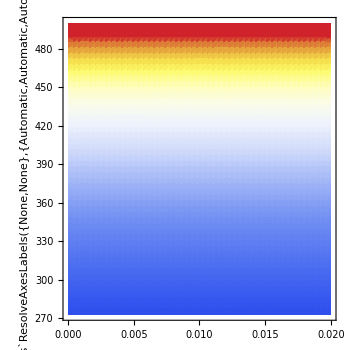
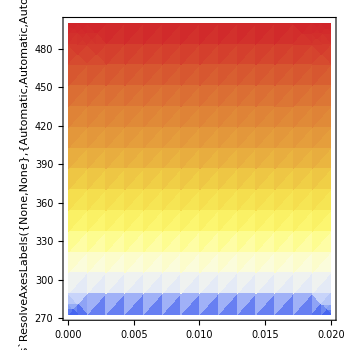
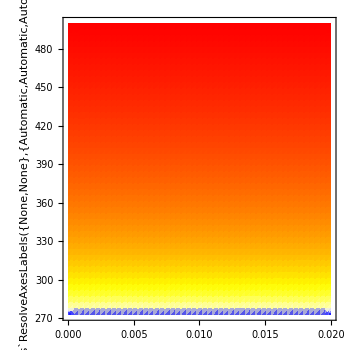
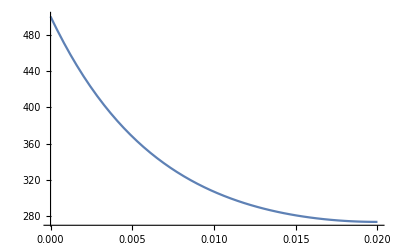
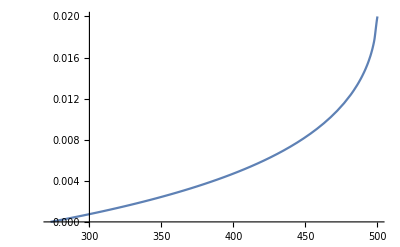
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
Module[{T,xT,RY,YW,WB,col1,col2},
T[x_]:=250+23.72*Cosh[152.3*(1/50-x)];
xT:=Evaluate@Interpolation[Transpose[{Range[500,273,-1],Evaluate@Table[x/.Quiet@FindRoot[250+23.72*Cosh[152.3*(1/50-x)]==t,{x,0}],{t,273,500,1}]}]];

RY=Table[RGBColor[1,i/2,0],{i,0,2,0.05}];
YW=Table[RGBColor[1,1,i/2],{i,0.1,1.8,0.1}];
WB=Table[RGBColor[1-i,1-i,1],{i,0.1,1,0.1}];

(*col1[x_]:=Blend[Reverse[Join[RY,YW,WB]],Rescale[T[x],{T[0.02],T[0]}]];*)
(*col1[x_]:=Blend[Reverse[Join[RY,YW,WB]],Rescale[xT[T[x]],{0.02,0}]];*)
col1[x_]:=Blend[Reverse[Join[RY,YW,WB]],Rescale[xT[T[x]],{0.02,0}]];
(*col2[x_]:=ColorData["TemperatureMap"][Rescale[T[x],{T[0.02],T[0]}]];*)
col2[x_]:=ColorData["TemperatureMap"][Rescale[xT[T[x]],{0.02,0}]];

(*Grid[{{
DensityPlot[xT[y],{x,0,1},{y,273,500},ColorFunction->(col2[#1]&),ColorFunctionScaling->False,ImageSize->{350,350},PlotPoints->30](*,
DensityPlot[x,{x,0,0.02},{y,273,500},ColorFunction->(col2[#]&),ColorFunctionScaling->False,ImageSize->{350,350}]*)
}}]*)
Grid[{{
Show[
DensityPlot[xT[y],{x,0,0.02},{y,273,490},ColorFunction->"TemperatureMap",PlotPoints->50],
DensityPlot[xT[500],{x,0,0.02},{y,490,500},ColorFunction->ColorData[{"TemperatureMap","Reverse"}],PlotPoints->50],
ImageSize->{350,350},PlotRange->{{0,0.02},{273,500}}],
DensityPlot[xT[y],{x,0,0.02},{y,273,500},ColorFunction->(col2[#1]&),ColorFunctionScaling->False,ImageSize->{350,350}],
DensityPlot[xT[y],{x,0,0.02},{y,273,500},ColorFunction->(col1[#]&),ColorFunctionScaling->False,PlotPoints->50,ImageSize->{350,350}]
(*DensityPlot[xT[y],{x,0,0.02},{y,273,500},ColorFunction->Function[{x,y},col1[y]],ColorFunctionScaling->False,PlotPoints->50,ImageSize->{350,350}]*)
},
{Plot[T[x],{x,0,0.02}],Plot[xT[x],{x,273,500}]}
}]
]
```